```mathematica
(* 8D *)
eqs={x1'[t]==τ1 (x2[t]-x1[t])+x4[t],x2'[t]==τ2 x1[t]-x1[t] x3[t]+x4[t],x3'[t]==x1[t] x2[t]-x3[t]-x4[t]+x7[t],x4'[t]==-τ3 (x1[t]+x2[t])+x5[t],x5'[t]==-x2[t]-τ4 x4[t]+x6[t],x6'[t]==-τ5 (x1[t]+x5[t])+τ4 x7[t],x7'[t]==-τ6 (x1[t]+x6[t]-x8[t]),x8'[t]==-τ7 x7[t]};

(* Initial conditions*)
init={x1[0]==1.1,x2[0]==1.1,x3[0]==1.1,x4[0]==1.1,x5[0]==0,x6[0]==0,x7[0]==0,x8[0]==0};

(* Parameter values& time settings *)
params={τ1->11,τ2->75,τ3->2,τ4->0.2,τ5->0.1,τ6->0.1,τ7->0.2};
tMax=200;
tTrans=50;

(* Solve for the eight InterpolatingFunction objects *)
solFuns=NDSolveValue[Join[eqs/. params,init],(*equations+initials with τ replacements*){x1,x2,x3,x4,x5,x6,x7,x8},(*return these 8 functions*){t,0,tMax},(*time domain*)MaxSteps->Infinity];

(* Unpack them into named functions *)
{x1fun,x2fun,x3fun,x4fun,x5fun,x6fun,x7fun,x8fun}=solFuns;
```

-Graphics3D-

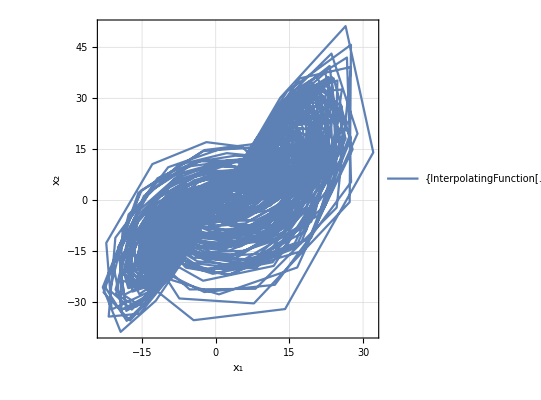

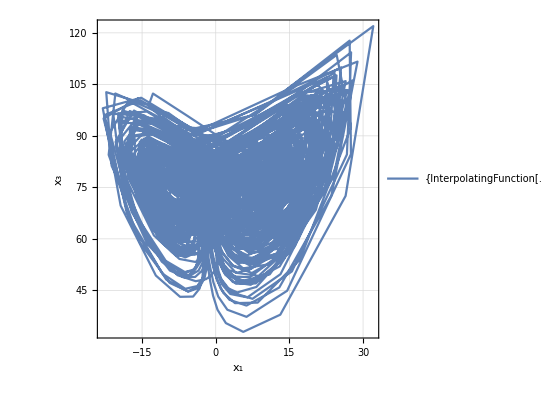

-Graphics3D-

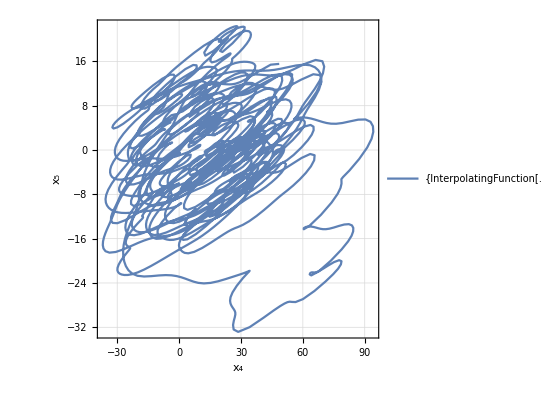

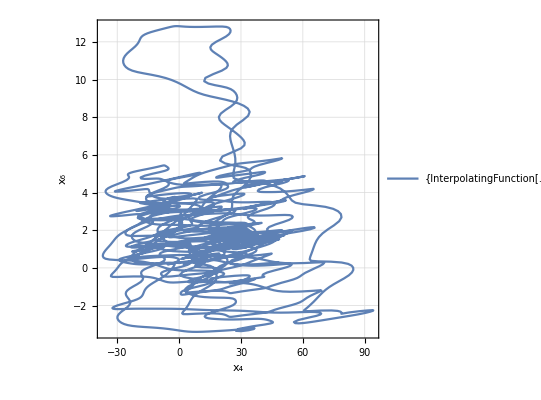

-Graphics3D-

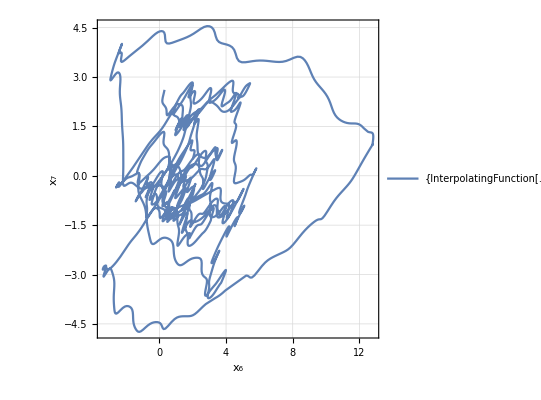

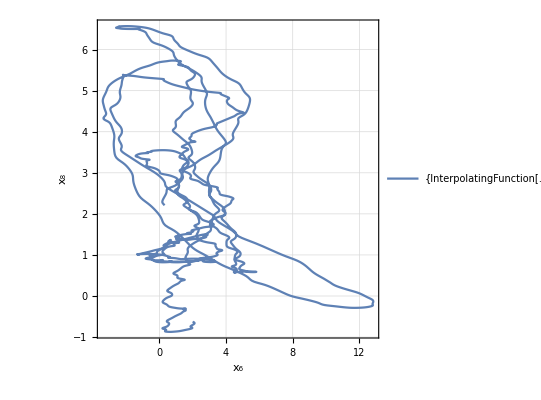

```mathematica
p123=ParametricPlot3D[{x1fun[t],x2fun[t],x3fun[t]},{t,tTrans,tMax},PlotStyle->Thin,AxesLabel->{"x₁","x₂","x₃"},BoxRatios->{1,1,1}]
p12=ParametricPlot[Evaluate[{x1fun[t],x2fun[t]}],{t,tTrans,tMax},AspectRatio->1,Frame->True,FrameLabel->{"x₁","x₂"},PlotTheme->"Detailed"]
p13=ParametricPlot[Evaluate[{x1fun[t],x3fun[t]}],{t,tTrans,tMax},AspectRatio->1,Frame->True,FrameLabel->{"x₁","x₃"},PlotStyle->Thick,PlotTheme->"Detailed"]

p456=ParametricPlot3D[{x4fun[t],x5fun[t],x6fun[t]},{t,tTrans,tMax},PlotStyle->Thin,AxesLabel->{"x₄","x₅","x₆"},BoxRatios->{1,1,1},ImageSize->Medium]
p45=ParametricPlot[Evaluate[{x4fun[t],x5fun[t]}],{t,tTrans,tMax},AspectRatio->1,Frame->True,FrameLabel->{"x₄","x₅"},PlotStyle->Thick,PlotTheme->"Detailed"]
p46=ParametricPlot[Evaluate[{x4fun[t],x6fun[t]}],{t,tTrans,tMax},AspectRatio->1,Frame->True,FrameLabel->{"x₄","x₆"},PlotStyle->Thick,PlotTheme->"Detailed"]


p678=ParametricPlot3D[{x6fun[t],x7fun[t],x8fun[t]},{t,tTrans,tMax},PlotStyle->Thin,AxesLabel->{"x₆","x₇","x₈"},BoxRatios->{1,1,1},ImageSize->Medium]
p67=ParametricPlot[Evaluate[{x6fun[t],x7fun[t]}],{t,tTrans,tMax},AspectRatio->1,Frame->True,FrameLabel->{"x₆","x₇"},PlotStyle->Thick,PlotTheme->"Detailed"]
p68=ParametricPlot[Evaluate[{x6fun[t],x8fun[t]}],{t,tTrans,tMax},AspectRatio->1,Frame->True,FrameLabel->{"x₆","x₈"},PlotStyle->Thick,PlotTheme->"Detailed"]
```

```mathematica
orbitPoints[τ2val_,xN_Symbol]:=Module[{vars,init,params,eqs,sol,result,tMax=300,tTrans=250},vars={x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t]};
init=Thread[(vars/. t->0)=={1.1,1.1,1.1,1.1,0,0,0,0}];
params={τ1->11,τ2->τ2val,τ3->2,τ4->0.2,τ5->0.1,τ6->0.1,τ7->0.2};
eqs={x1'[t]==τ1 (x2[t]-x1[t])+x4[t],x2'[t]==τ2 x1[t]-x1[t] x3[t]+x4[t],x3'[t]==x1[t] x2[t]-x3[t]-x4[t]+x7[t],x4'[t]==-τ3 (x1[t]+x2[t])+x5[t],x5'[t]==-x2[t]-τ4 x4[t]+x6[t],x6'[t]==-τ5 (x1[t]+x5[t])+τ4 x7[t],x7'[t]==-τ6 (x1[t]+x6[t]-x8[t]),x8'[t]==-τ7 x7[t]}/. params;
Check[sol=NDSolveValue[Join[eqs,init],vars,{t,0,tMax},MaxSteps->Infinity];
Table[{τ2val,Evaluate[xN[t]/. Thread[vars->sol]]},{t,tTrans,tMax,0.5}],{} (*fallback on failure*)]]
```

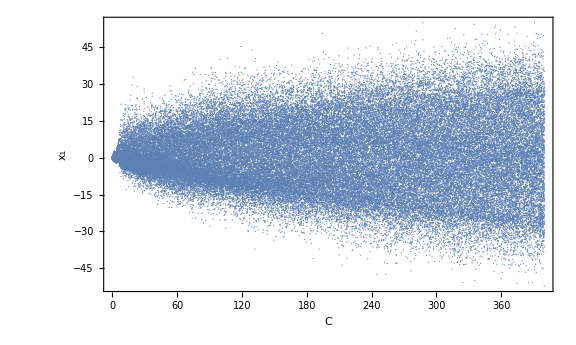

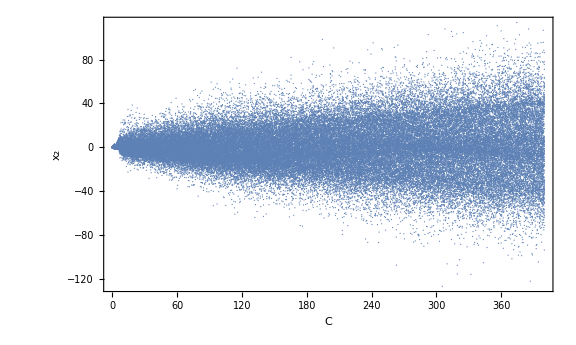

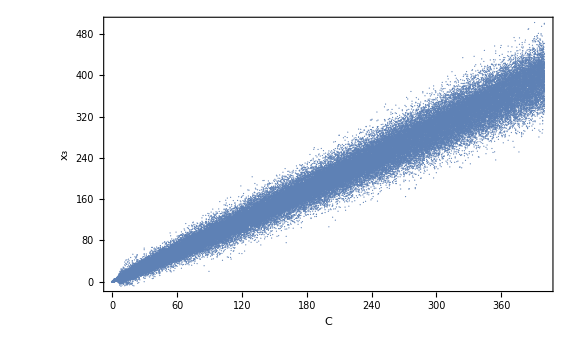

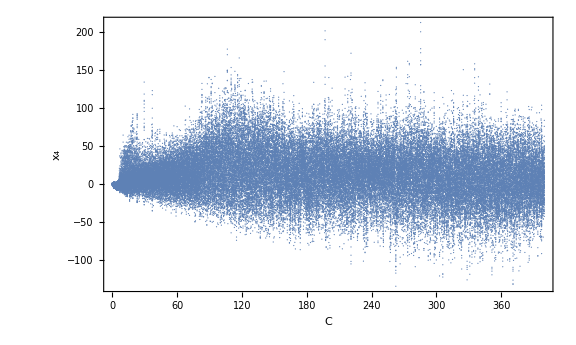

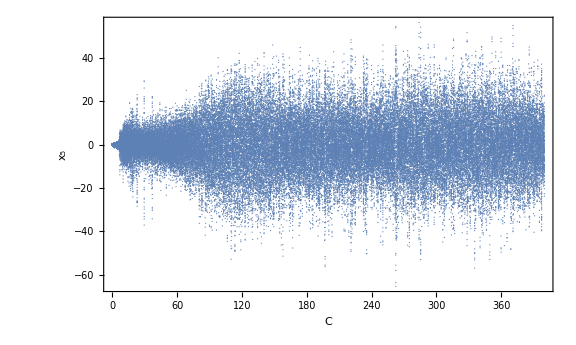

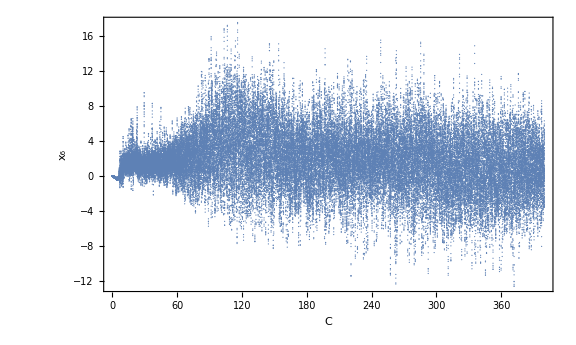

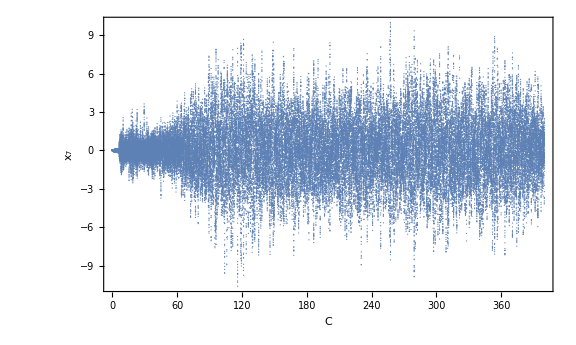

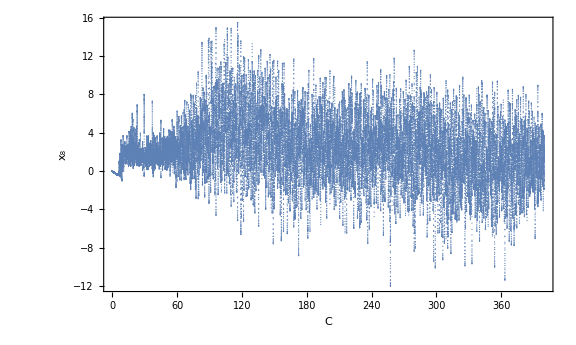

```mathematica
(*Define τ2 range*)τ2Vals=Range[0,400,0.5];

(*Generate datasets for each variable*)
dataX1=Table[orbitPoints[τ2,x1],{τ2,τ2Vals}];
dataX2=Table[orbitPoints[τ2,x2],{τ2,τ2Vals}];
dataX3=Table[orbitPoints[τ2,x3],{τ2,τ2Vals}];
dataX4=Table[orbitPoints[τ2,x4],{τ2,τ2Vals}];
dataX5=Table[orbitPoints[τ2,x5],{τ2,τ2Vals}];
dataX6=Table[orbitPoints[τ2,x6],{τ2,τ2Vals}];
dataX7=Table[orbitPoints[τ2,x7],{τ2,τ2Vals}];
dataX8=Table[orbitPoints[τ2,x8],{τ2,τ2Vals}];

pointsX1=Flatten[dataX1,1];
pointsX2=Flatten[dataX2,1];
pointsX3=Flatten[dataX3,1];
pointsX4=Flatten[dataX4,1];
pointsX5=Flatten[dataX5,1];
pointsX6=Flatten[dataX6,1];
pointsX7=Flatten[dataX7,1];
pointsX8=Flatten[dataX8,1];

(*Plot each bifurcation diagram*)
ListPlot[pointsX1,PlotStyle->PointSize[0.0015],Frame->True,FrameLabel->{"C","x₁"},PlotRange->All,AspectRatio->0.6,ImageSize->Large]
ListPlot[pointsX2,PlotStyle->PointSize[0.0015],Frame->True,FrameLabel->{"C","x₂"},PlotRange->All,AspectRatio->0.6,ImageSize->Large]
ListPlot[pointsX3,PlotStyle->PointSize[0.0015],Frame->True,FrameLabel->{"C","x₃"},PlotRange->All,AspectRatio->0.6,ImageSize->Large]
ListPlot[pointsX4,PlotStyle->PointSize[0.0015],Frame->True,FrameLabel->{"C","x₄"},PlotRange->All,AspectRatio->0.6,ImageSize->Large]
ListPlot[pointsX5,PlotStyle->PointSize[0.0015],Frame->True,FrameLabel->{"C","x₅"},PlotRange->All,AspectRatio->0.6,ImageSize->Large]
ListPlot[pointsX6,PlotStyle->PointSize[0.0015],Frame->True,FrameLabel->{"C","x₆"},PlotRange->All,AspectRatio->0.6,ImageSize->Large]
ListPlot[pointsX7,PlotStyle->PointSize[0.0015],Frame->True,FrameLabel->{"C","x₇"},PlotRange->All,AspectRatio->0.6,ImageSize->Large]
ListPlot[pointsX8,PlotStyle->PointSize[0.0015],Frame->True,FrameLabel->{"C","x₈"},PlotRange->All,AspectRatio->0.6,ImageSize->Large]
```